## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/primary-repos/github/experiment-mathematica/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="rcs/fourier/visuals/";  
Get["utility modules.m",Path->dirPack];
Get["rcs-tools-01.m",Path->dirnb<>"rcs/tools/"];
Needs["PlotLegends`"]
stamp1;
```

CreateDirectory::filex: /Users/dantopa/primary-repos/github/experiment-mathematica/io/ already exists.

CreateDirectory::filex: /Users/dantopa/primary-repos/github/experiment-mathematica/io/rcs/ already exists.

CreateDirectory::filex: /Users/dantopa/primary-repos/github/experiment-mathematica/io/rcs/fourier/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

maximum memory: 0.378661 GB

seed file: /Users/dantopa/primary-repos/github/experiment-mathematica/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.1.0 for Mac OS X x86

date: May 11, 2020, time: 19:11:00

nb: /Users/dantopa/primary-repos/github/experiment-mathematica/nb/rcs/fourier/visuals/panel-plot-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.378661 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,5},{Automatic,5}};
```

```mathematica
isize=ImageSize->5 72;
```

```mathematica
ftickspi={{-π,-180°},{-π/2,-90°},{0,"0°"},{π/2,90°},{π,180°}};
```

```mathematica
optA={ipad,Frame->True,FrameLabel->{labelyaw,labelrcs},FrameTicks->{{Automatic,Automatic},{fticks180,Automatic}}};
```

#### functions

#### substitutions

#### modules

#### tagger

```mathematica
Clear[tagSource];
tagSource[str_OutputStream,comment_String]:=Module[{},
(* tag Mathematica file *)
Write[str,comment,nb];
Write[str,comment,dirHome];
mark;
Write[str,comment,"user: ",user,", CPU: ",CPU,", MM v. ",mmv];
Write[str,comment,time," ",date];
Write[str,""];
]
```

## import

```mathematica
meanRCS=Import[dirDataLocker<>sciaccarcs];
```

```mathematica
mx=Max[meanRCS]
mn=Min[meanRCS]
```

59.2522

0.798997

## sort plots

### functions

```mathematica
νticks={{1,3},{8,10},{18,20},{28,30}};
λticks={{1,100},{15,20},{4,50},{28,10}};θticks={{1,0},{91,π/4},{181,π/2},{271,(3π)/4},{361,2π}};
θticks={{1,0},{91,90},{181,180},{271,270},{361,360}};
```

```mathematica
θticks={{1,"-180°"},{91,"-90°"},{181,"0°"},{271,"90°"},{361,"180°"}};
```

```mathematica
Clear[fticks];
fticks:={{Automatic,Automatic},{θticks,Automatic}};
```

```mathematica
Clear[myMatrixPlot];
myMatrixPlot[ψ_,str_String,options___]:=Module[{g},
g=MatrixPlot[ψ,
options,
PlotLabel->str,
ColorFunction->(Hue[(1-Rescale[#,{mn,mx}])magicnumber]&),
ColorFunctionScaling->False,
FrameTicks->{{νticks,λticks},{θticks,None}},
FrameLabel->{"Frequency, MHz","Azimuth","Wavelength, m",None},
PlotLegends->Placed[Automatic,After],
ImageSize->6 72,
AspectRatio->1/GoldenRatio];
Return[g];
]
```

```mathematica
Clear[myArrayPlot];
myArrayPlot[ψ_,str_String,options___]:=Module[{g},
g=ArrayPlot[ψ,
options,
PlotLabel->str,
ColorFunction->(Hue[(1-Rescale[#,{mn,mx}])magicnumber]&),
ColorFunctionScaling->False,
FrameTicks->{{νticks,λticks},{θticks,None}},
FrameLabel->{"Frequency, MHz","Azimuth","Wavelength, m",None},
PlotLegends->Placed[Automatic,After],
ImageSize->6 72,
AspectRatio->1/GoldenRatio];
Return[g];
]
```

### plots

```mathematica
gmatrixplot=myMatrixPlot[meanRCS,"Sciacca AirFrame Mean Total RCS"]
```

MatrixPlot::mat0: Argument meanRCS at position 1 is not a matrix.

MatrixPlot[meanRCS,PlotLabel→Sciacca AirFrame Mean Total RCS,ColorFunction→(Hue[(1-Rescale[#1,{mn,mx}]) magicnumber]&),ColorFunctionScaling→False,FrameTicks→{{{{1,3},{8,10},{18,20},{28,30}},{{1,100},{15,20},{4,50},{28,10}}},{{{1,-180°},{91,-90°},{181,0°},{271,90°},{361,180°}},None}},FrameLabel→{Frequency, MHz,Azimuth,Wavelength, m,None},PlotLegends→Placed[Automatic,After],ImageSize→432,AspectRatio→1/GoldenRatio]

```mathematica
garrayplot=myArrayPlot[meanRCS,"Sciacca AirFrame Mean Total RCS"]
```

ArrayPlot::mat: Argument meanRCS at position 1 is not a list of lists.

ArrayPlot[meanRCS,PlotLabel→Sciacca AirFrame Mean Total RCS,ColorFunction→(Hue[(1-Rescale[#1,{mn,mx}]) magicnumber]&),ColorFunctionScaling→False,FrameTicks→{{{{1,3},{8,10},{18,20},{28,30}},{{1,100},{15,20},{4,50},{28,10}}},{{{1,-180°},{91,-90°},{181,0°},{271,90°},{361,180°}},None}},FrameLabel→{Frequency, MHz,Azimuth,Wavelength, m,None},PlotLegends→Placed[Automatic,After],ImageSize→432,AspectRatio→1/GoldenRatio]

## export

```mathematica
multiExport["watercolor-array",garrayplot];multiExport["watercolor-matrix",gmatrixplot];
```

## row

```mathematica
grow=garrayplot=ArrayPlot[meanRCS,
PlotLabel->"Sciacca AirFrame Mean Total RCS",
ColorFunction->(Hue[(1-Rescale[#,{mn,mx}])magicnumber]&),
ColorFunctionScaling->False,
FrameTicks->{{νticks,λticks},{θticks,None}},
FrameLabel->{"Frequency, MHz","Azimuth","Wavelength, m",None},
ImageSize->6 72,
AspectRatio->1/GoldenRatio,
Epilog->myBox]
```

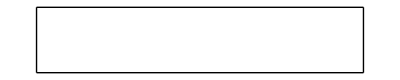

```mathematica
{xleft,xright}={-25,385};
{ybot,ytop}={-0.1,1.3};
myBox=Graphics[{Thick,
Line[{{xleft,ybot},{xright,ybot}}],
Line[{{xright,ybot},{xright,ytop}}],
Line[{{xleft,ytop},{xright,ytop}}],
Line[{{xleft,ytop},{xleft,ybot}}]}]
```

```mathematica
myBox={Thick,
Line[{{xleft,ybot},{xright,ybot}}],
Line[{{xright,ybot},{xright,ytop}}],
Line[{{xleft,ytop},{xright,ytop}}],
Line[{{xleft,ytop},{xleft,ybot}}]}
```

{Thickness[Large],Line[{{-25,-0.1},{385,-0.1}}],Line[{{385,-0.1},{385,1.3}}],Line[{{-25,1.3},{385,1.3}}],Line[{{-25,1.3},{-25,-0.1}}]}

## column

```mathematica
gcol=garrayplot=ArrayPlot[meanRCS,
PlotLabel->"Sciacca AirFrame Mean Total RCS",
ColorFunction->(Hue[(1-Rescale[#,{mn,mx}])magicnumber]&),
ColorFunctionScaling->False,
FrameTicks->{{νticks,λticks},{θticks,None}},
FrameLabel->{"Frequency, MHz","Azimuth","Wavelength, m",None},
ImageSize->6 72,
AspectRatio->1/GoldenRatio,
Epilog->myBox]
```

```mathematica
{xleft,xright}={87,93};
{ybot,ytop}={0,28};
myBox={Thickness[0.0075],Gray,
Line[{{xleft,ybot},{xright,ybot}}],
Line[{{xright,ybot},{xright,ytop}}],
Line[{{xleft,ytop},{xright,ytop}}],
Line[{{xleft,ytop},{xleft,ybot}}]}
```

{Thickness[0.0075],GrayLevel[0.5],Line[{{87,0},{93,0}}],Line[{{93,0},{93,28}}],Line[{{87,28},{93,28}}],Line[{{87,28},{87,0}}]}

```mathematica
multiExport["rcs-col",gcol];
multiExport["rcs-row",grow];
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```